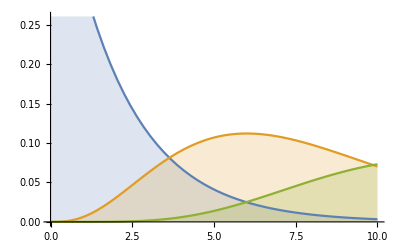

```mathematica
Plot[Evaluate@Table[PDF[GammaDistribution[α,2],x],{α,{1,4,7}}],{x,0,10},Filling->Axis]
```

```mathematica
Gamma[7,2]
```

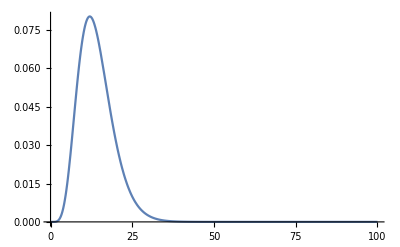

```mathematica
Plot[PDF[GammaDistribution[7,2],x],{x,0,100},PlotRange->Full]
```

```mathematica
Plot[PDF[GammaDistribution[7,2],x],{x,0,100},PlotRange->Full]
```

```mathematica
b=[RandomVariate[GammaDistribution[7,2]]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[PDF[RandomVariate[GammaDistribution[7,2]]]]

```mathematica
a=Exp[-RandomVariate[GammaDistribution[7,2],8]*RandomReal[]]
```

{0.00327553,5.56231×10^-6,0.0000122389,0.000791626,0.0000864916,0.000102442,0.00181827,5.35919×10^-6}

```mathematica
Times@@a[[1;;4]]
```

1.2568×10^-13

```mathematica
Times@@a[[5;;8]]
```

7.75908×10^-22

```mathematica
RandomVariate[GammaDistribution[7,2]]
```

34.2064

```mathematica
Log[1]
```

0

```mathematica
Log[0]
```

-∞

```mathematica
Log[0.000000001]
```

-20.7233

```mathematica
Log[0.001]
```

-6.90776

```mathematica
Plot[PDF[DirichletDistribution[{1,1,1}],{a,b}],{{a,0,1},{b,0,1}}]
```

Plot::pllim: Range specification {{a, 0, 1}, {b, 0, 1}} is not of the form {x, xmin, xmax}.

Plot[PDF[DirichletDistribution[{1,1,1}],{a,b}],{{a,0,1},{b,0,1}}]

```mathematica
a=RandomVariate[DirichletDistribution[{1,1,1,1}]]
last=1-Total@a
```

{0.399726,0.159739,0.215119}

0.225416

```mathematica
Total[a]
```

0.718471

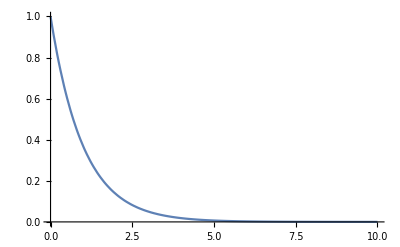

```mathematica
Plot[PDF[GammaDistribution[1,1],x],{x,0,10},PlotRange->Full]
```

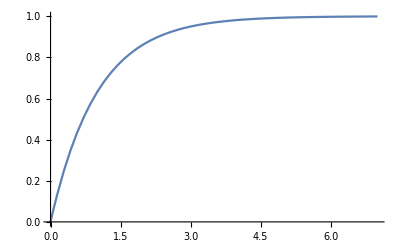

```mathematica
Plot[CDF[GammaDistribution[1,1],x],{x,0,7},PlotRange->Full]
```

```mathematica
-Log[0.001]
```

6.90776

```mathematica
1.*^3
```

1000.

```mathematica
RandomSample[Range[10]]-1
```

{1,2,0,9,8,6,7,3,5,4}